```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pi/repos/HATS/testing/USSA76

```mathematica
tpr=ReadList["TPRho.tst",Number,RecordLists->True];
```

```mathematica
tpr[[1]]
tpr[[85507]]
tpr[[86007]]
```

{0.,288.15,101325.,1225.}

{85.5,187.852,0.408018,0.0075639}

{86.,186.867,0.000373383,0.00695788}

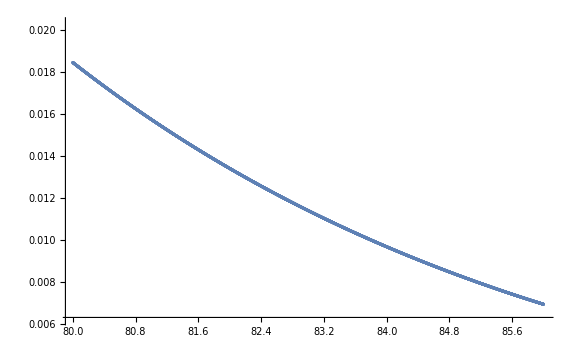

```mathematica
ListPlot[
tpr[[80007;;86007,1;;4;;3]],
PlotRange->{0.9*Min[tpr[[80007;;86007,4]]],1.1*Max[tpr[[80007;;86007,4]]]},ImageSize->Large]
```

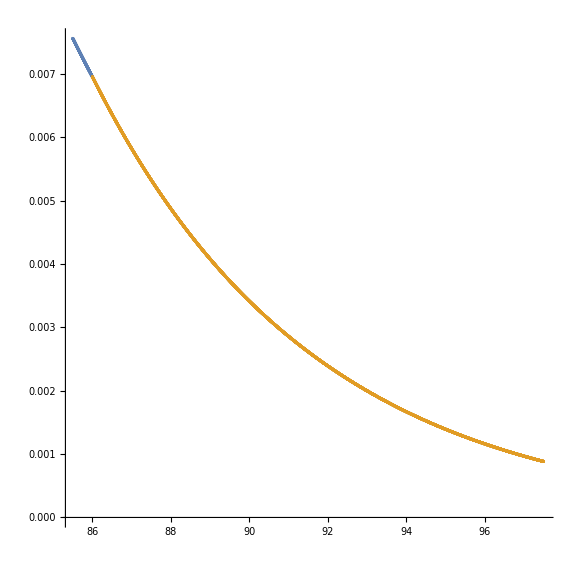

```mathematica
ListPlot[
{
tpr[[85507;;86007,1;;4;;3]],
tpr[[86007;;97507,1;;4;;3]]
},
ImageSize->Large,AspectRatio->1]
```

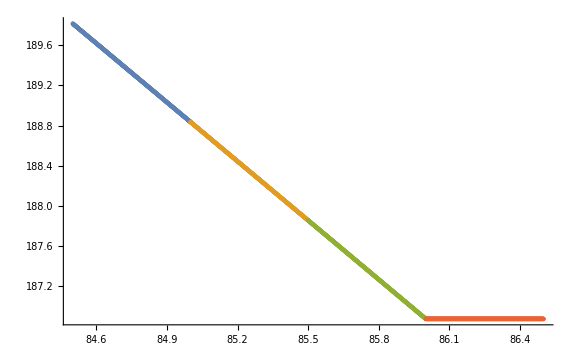

```mathematica
ListPlot[
{
tpr[[84507;;85007,1;;2]],
tpr[[85007;;85507,1;;2]],
tpr[[85507;;86007,1;;2]],
tpr[[86007;;86507,1;;2]]
},
ImageSize->Large]
```